## Metricas del fluido perfecto e indice del politropo

```mathematica
ξ[r_]:=Log[(A-(B)*(r^2))^2];
μ[r_]:=-Log[1+(c)(r^2)((A)-3(r^2)(B))^(-2/3)];
Γ:=1+1/n
```

## Ecuación diferencial master para la obtención de la deformación del espacio f

```mathematica
DSolve[f'[r]/r+f[r]/r^2==-(Ka)^(Γ)(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)),f[r],r]
```

{{f[r]→(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))+C[1]/r}}

```mathematica
f[r_]:=(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))
```

## Ecuación diferencial para la obtención de la derivada de la deformación del tiempo

```mathematica
gprime[r_]:=(r/(Exp[-μ[r]]+f[r]))(κ Ka((Ka)^(Γ)/κ(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)))^(Γ) -f[r](1/r^2+ξ'[r]/r))
```

```mathematica
gprime[r]//FullSimplify
```

(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
gprime[r_]:=(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

```mathematica
gprime[r]/.{M->u R,r->x R}//FullSimplify
```

(x (2.1758×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3.+((-0.9-1.92371 √(1-2. u))^(2/3) u (-0.0344575+0.147302 √(1-2. u)+0.172287 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (-0.233923+1. √(1-2. u)+0.233923 x^2))))/(1-(2. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2)/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3)))

```mathematica
gprimeg[x_]:=(x (2.1757973070786907*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3.+((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.034457497120008104+0.1473024260148382 √(1-2. u)+0.17228748560004054 x^2))/((0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2))))/(1-(2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2)/((0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3)))
```

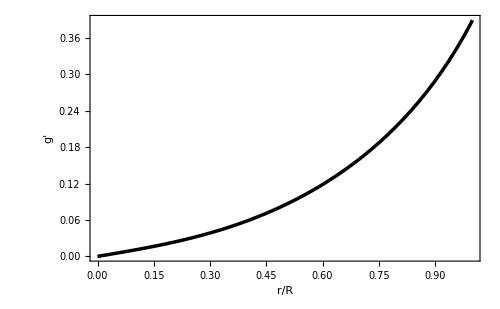

```mathematica
solu1:=Re[gprimeg[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","g'"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

## Cambio en la geometria del espacio-tiempo

### Derivada de ν, para el tiempo

```mathematica
νprime[r_]:=D[ξ[r],r]+gprime[r]
νprime[r]//FullSimplify
```

-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
νprime[r_]:=-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

### Cambio de λ, para el espacio

```mathematica
λ[r_]:=-Log[Exp[-μ[r]]+f[r]]
```

```mathematica
λ[r]//FullSimplify
```

-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))]

```mathematica
λ[r_]:=-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))];
```

## Ecuaciones de Einstein

### Densidad Efectiva

```mathematica
ρ[r_]:=1/(κ r^2)(1-ⅇ^(-λ[r])(1-r D[λ[r],r]));
ρ[r]//FullSimplify
```

-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ)

```mathematica
ρ[r_]:=-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ);
```

### Presión efectiva

```mathematica
Pr[r_]:=-1/(κ r^2)(1-ⅇ^(-λ[r])(1+r *νprime[r]));
Pr[r]//FullSimplify
```

1/((A-3 B r^2) (A-B r^2) κ)(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)

```mathematica
Pr[r_]:=1/((A-3 B r^2) (A-B r^2) κ)(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)
```

### Presión Tangencial efectiva

```mathematica
Pt[r_]:=Exp[-λ[r]]/(4κ)(2νprime'[r]+(νprime[r])^2-λ'[r]νprime[r]+(2(νprime[r]-λ'[r]))/r);
Pt[r]//Simplify
```

((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)

```mathematica
Pt[r_]:=((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)
```

## Resolución de la integral numérica de gprima, mediante MATLAB

```mathematica
gnume:=-1.308507
```

```mathematica
νnumer[r_]:=ξ[r]+gnume
```

## Aplicación de las condiciones de frontera

```mathematica
Solve[Exp[-λ[R]]==1-(2M)/R,c]
```

{{c→-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)}}

```mathematica
c:=-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)
```

```mathematica
NSolve[Exp[νnumer[R]]==1-(2M)/R,A]
```

{{A→1.93142×10^-8 (5.17755×10^7 B R^2-(9.96008×10^7 √(-2. M+R))/(√R))},{A→1.93142×10^-8 (5.17755×10^7 B R^2+(9.96008×10^7 √(-2. M+R))/(√R))}}

```mathematica
A:=1.9314167434324346*^-8 (5.1775465*^7 B R^2-(9.960076929537149*^7 √(-2. M+R))/(√R))
```

### Damos las constantes que usamos en la integración

```mathematica
B=0.45;
Ka=0.43;
n=0.5;
κ=8*π;
R=1;
```

```mathematica
Clear[A,B,c,Ka,n,κ,R]
```

## Intercambio Energético

```mathematica
DEnergy[r_]:=gprime[r]/(2κ)×Exp[-μ[r]]/r(ξ'[r]+μ'[r])
DEnergy[r]/.{M->u R,r->x R}//FullSimplify
```

-((1.02654×10^-8 x ((0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (-1.+4.2749 √(1-2. u)+1. x^2) (((-0.9-1.92371 √(1-2. u))^(2/3) u (-0.70177+3. √(1-2. u)+1.16962 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (-0.233923+1. √(1-2. u)+0.70177 x^2)))^3.+(-0.9-1.92371 √(1-2. u))^(2/3) u (-67700.4+289413. √(1-2. u)+338502. x^2)) (7.30992 (-0.9-1.92371 √(1-2. u))^(2/3) u^2+(0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (0.215901-0.922957 √(1-2. u)-0.647704 x^2)+(-0.9-1.92371 √(1-2. u))^(2/3) u (-3.85496+1.70996 √(1-2. u)-1.05469×10^-16 √(1-2. u) x^2+1. x^4)))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (0.233923-1. √(1-2. u)-0.233923 x^2)^2 (-0.233923+1. √(1-2. u)+0.70177 x^2) (-2. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2+1. (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3))))

```mathematica
DEnergy[x_]:=-((1.0265369805565476*^-8 x ((0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (-1.+4.274902077240703 √(1-2. u)+1. x^2) (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.7017704606549475+3. √(1-2. u)+1.1696174344249126 x^2))/((0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 x^2)))^3.+(-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-67700.43585200135+289412.7338538216 √(1-2. u)+338502.1792600068 x^2)) (7.309915107998749 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u^2+(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (0.21590139999999994-0.9229573433391758 √(1-2. u)-0.6477041999999998 x^2)+(-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-3.8549575539993746+1.7099608308962808 √(1-2. u)-1.0546877142601192*^-16 √(1-2. u) x^2+0.9999999999999999 x^4)))/((0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (0.2339234868849825-1. √(1-2. u)-0.2339234868849825 x^2)^2 (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 x^2) (-2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2+1. (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3))))
```

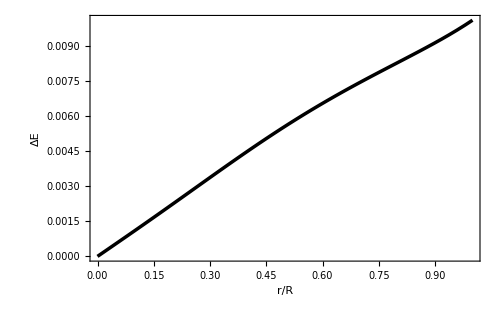

```mathematica
solu1:=Re[DEnergy[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ΔE"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
DEnergy[x]/.{x->√(x^2+y^2)}//FullSimplify
```

-((1.02654×10^-8 √(x^2+y^2) ((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-1.+4.2749 √(1-2. u)+1. (x^2+y^2)) (((-0.9-1.92371 √(1-2. u))^(2/3) u (-0.70177+3. √(1-2. u)+1.16962 (x^2+y^2)))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.233923+1. √(1-2. u)+0.70177 (x^2+y^2))))^3.+(-0.9-1.92371 √(1-2. u))^(2/3) u (-67700.4+289413. √(1-2. u)+338502. (x^2+y^2))) (7.30992 (-0.9-1.92371 √(1-2. u))^(2/3) u^2+(0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.215901-0.922957 √(1-2. u)-0.647704 (x^2+y^2))+(-0.9-1.92371 √(1-2. u))^(2/3) u (-3.85496+1.70996 √(1-2. u)-1.05469×10^-16 √(1-2. u) (x^2+y^2)+1. (x^2+y^2)^2)))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.233923-1. √(1-2. u)-0.233923 (x^2+y^2))^2 (-0.233923+1. √(1-2. u)+0.70177 (x^2+y^2)) (-2. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)+1. (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))

```mathematica
dEnergy[x_,y_]:=-((1.0265369805565476*^-8 √(x^2+y^2) ((0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-1.+4.274902077240703 √(1-2. u)+1. (x^2+y^2)) (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.7017704606549475+3. √(1-2. u)+1.1696174344249126 (x^2+y^2)))/((0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 (x^2+y^2))))^3.+(-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-67700.43585200135+289412.7338538216 √(1-2. u)+338502.1792600068 (x^2+y^2))) (7.309915107998749 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u^2+(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.21590139999999994-0.9229573433391758 √(1-2. u)-0.6477041999999998 (x^2+y^2))+(-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-3.8549575539993746+1.7099608308962808 √(1-2. u)-1.0546877142601192*^-16 √(1-2. u) (x^2+y^2)+0.9999999999999999 (x^2+y^2)^2)))/((0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.2339234868849825-1. √(1-2. u)-0.2339234868849825 (x^2+y^2))^2 (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 (x^2+y^2)) (-2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)+1. (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))
```

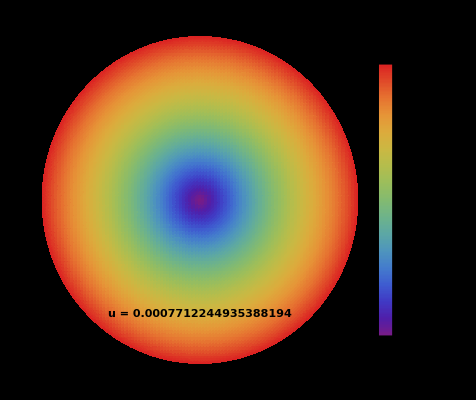

```mathematica
DensityPlot[Re[dEnergy[x,y]]/.{u->0.3340789749418907},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.3340789749418907",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Condiciones de aceptabilidad

### Sector material

```mathematica
Pr[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.0107518 (-0.81+3.46267 √(1-2. u)+2.43 x^2+8.05185×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.233923+1. √(1-2. u)+0.233923 x^2) (-0.233923+1. √(1-2. u)+0.70177 x^2)+(-0.9-1.92371 √(1-2. u))^(2/3) u (0.45-1.92371 √(1-2. u)-1.35 x^2)^(1/3) (-0.833714+3.56405 √(1-2. u)+4.16857 x^2)))/((-0.233923+1. √(1-2. u)+0.233923 x^2) (-0.233923+1. √(1-2. u)+0.70177 x^2))

```mathematica
Prg[x_]:=(0.010751839448809199 (-0.81+3.4626706825649696 √(1-2. u)+2.43 x^2+8.051852388522243*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2) (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 x^2)+(-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(1/3) (-0.8337139082933227+3.56404531838759 √(1-2. u)+4.1685695414666135 x^2)))/((-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2) (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 x^2))
```

```mathematica
Solve[Prg[1]==0,u]
```

{{u→-186.232},{u→0.334079},{u→0.496713},{u→177.768-8.80582 ⅈ},{u→177.768+8.80582 ⅈ}}

```mathematica
Prg[1]/.u->0.3340789749418907
```

2.05315×10^-13

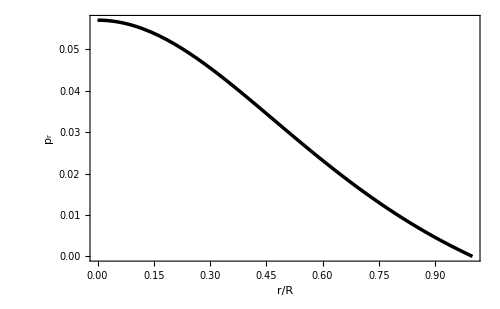

```mathematica
solu1:=Re[Prg[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Full]
```

```mathematica
Pt[r]/.{M-> u R, r->x R}//Simplify
```

(0.000363175 (1-(2. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2)/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3))) (-23.9802 x^2 (0.233923-1. √(1-2. u)-0.70177 x^2)^2 (1. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3))^2+51.2565 (0.233923-1. √(1-2. u)-0.70177 x^2)^2 (-0.233923+1. √(1-2. u)+0.233923 x^2) (1. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3))^2+0.265144 (-0.9-1.92371 √(1-2. u))^(2/3) u x^2 (-2. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2+(0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3)) (-7.11895 (-0.233923+1. √(1-2. u))^3-14.9876 (0.233923-1. √(1-2. u))^2 x^2-8.95966 (-0.233923+1. √(1-2. u)) x^4-1.36688 x^6+14.2379 (-0.233923+1. √(1-2. u)) (0.233923-1. √(1-2. u)-0.70177 x^2)^2-0.00157731 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^2. (-0.233923+1. √(1-2. u)+0.233923 x^2)^3)+0.5 x^2 (0.45-1.92371 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9-1.92371 √(1-2. u))^(2/3) u x^2-1.8 (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3)-4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (-0.233923+1. √(1-2. u)+0.233923 x^2)-0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 x^2))^2-4. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2 (0.45-1.92371 √(1-2. u)-1.35 x^2) (0.45-1.92371 √(1-2. u)-0.45 x^2)^2 (4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (-0.233923+1. √(1-2. u)+0.233923 x^2)+0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 x^2))-1. (0.45-1.92371 √(1-2. u)-1.35 x^2)^2 (0.45-1.92371 √(1-2. u)-0.45 x^2) (-2. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2+(0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3)) (4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (-0.233923+1. √(1-2. u)+0.233923 x^2)+0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 x^2))+2. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2 (0.45-1.92371 √(1-2. u)-1.35 x^2) (0.45-1.92371 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9-1.92371 √(1-2. u))^(2/3) u x^2+1.8 (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3)+4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (-0.233923+1. √(1-2. u)+0.233923 x^2)+0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 x^2))-1. (0.45-1.92371 √(1-2. u)-1.35 x^2) (0.45-1.92371 √(1-2. u)-0.45 x^2) (-2. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2+(0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3)) (14.8026 (-0.9-1.92371 √(1-2. u))^(2/3) u (0.233923-1. √(1-2. u)-0.233923 x^2)^2+6.92534 (-0.233923+1. √(1-2. u)+0.70177 x^2) (1. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-1.92371 √(1-2. u)-1.35 x^2) (4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (-0.233923+1. √(1-2. u)+0.233923 x^2)+0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 x^2)))))/((0.233923-1. √(1-2. u)-0.70177 x^2)^2 (0.233923-1. √(1-2. u)-0.233923 x^2)^2 (1. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3))^2)

```mathematica
Ptg[x_]:=(0.00036317455583588634 (1-(2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2)/((0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3))) (-23.980176511789907 x^2 (0.2339234868849825-1. √(1-2. u)-0.7017704606549475 x^2)^2 (1. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3))^2+51.25645319142468 (0.2339234868849825-1. √(1-2. u)-0.7017704606549475 x^2)^2 (-0.23392348688498252+1. √(1-2. u)+0.23392348688498252 x^2) (1. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3))^2+0.26514436682670883 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2 (-2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2+(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3)) (-7.118951832142317 (-0.2339234868849825+1. √(1-2. u))^3-14.987610319868688 (0.2339234868849825-1. √(1-2. u))^2 x^2-8.95966039113686 (-0.2339234868849825+1. √(1-2. u)) x^4-1.366875 x^6+14.237903664284634 (-0.2339234868849825+1. √(1-2. u)) (0.2339234868849825-1. √(1-2. u)-0.7017704606549475 x^2)^2-0.0015773056131510555 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^2. (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2)^3)+0.5 x^2 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2-1.8 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3)-4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2)-0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 x^2))^2-4. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2) (0.45-1.9237059347583163 √(1-2. u)-0.45 x^2)^2 (4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2)+0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 x^2))-1. (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^2 (0.45-1.9237059347583163 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2+(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3)) (4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2)+0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 x^2))+2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2) (0.45-1.9237059347583163 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2+1.8 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3)+4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2)+0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 x^2))-1. (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2) (0.45-1.9237059347583163 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2+(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3)) (14.80257809369747 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.2339234868849825-1. √(1-2. u)-0.2339234868849825 x^2)^2+6.925341365129939 (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 x^2) (1. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2) (4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2)+0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 x^2)))))/((0.2339234868849825-1. √(1-2. u)-0.7017704606549475 x^2)^2 (0.2339234868849825-1. √(1-2. u)-0.2339234868849825 x^2)^2 (1. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3))^2)
```

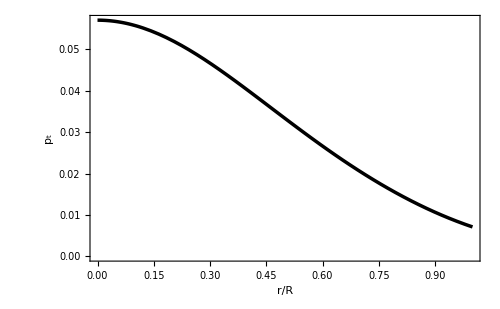

```mathematica
solu1:=Re[Ptg[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
ρ[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.0795775 (-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3))

```mathematica
ρg[x_]:=(0.07957747154594767 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3)
```

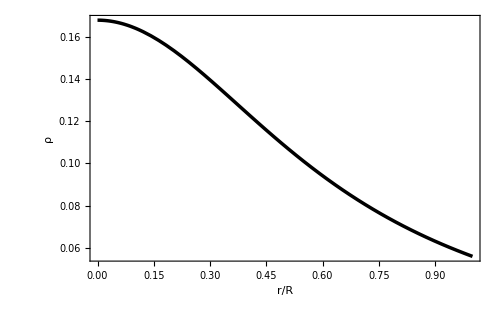

```mathematica
solu1:=Re[ρg[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Gráficas de componentes métricas del espacio-tiempo

```mathematica
Exp[νnumer[r]]/.{M->u R,r->x R}//FullSimplify
```

1. (0.233923-1. √(1-2. u)-0.233923 x^2)^2

```mathematica
metric1[x_]:=1. (0.2339234868849825-1. √(1-2. u)-0.2339234868849825 x^2)^2
```

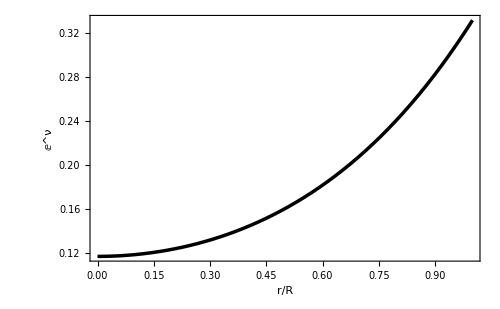

```mathematica
solu1:=Re[metric1[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^ν"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Exp[-λ[r]]/.{M-> u R, r->x R}//FullSimplify
```

1-(2. (-0.9-1.92371 √(1-2. u))^(2/3) u x^2)/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3))

```mathematica
metric2[x_]:=1-(2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u x^2)/((0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3))
```

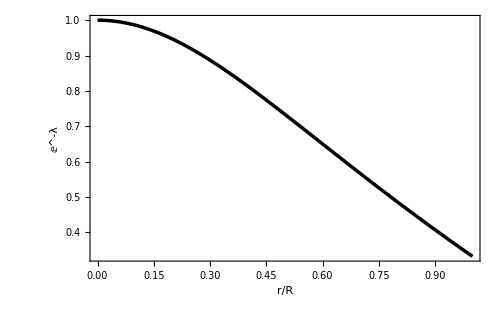

```mathematica
solu1:=Re[metric2[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^-λ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condiciones de energía

#### Condición de energía dominante

```mathematica
dec1[x_]:=ρg[x]-Prg[x];
```

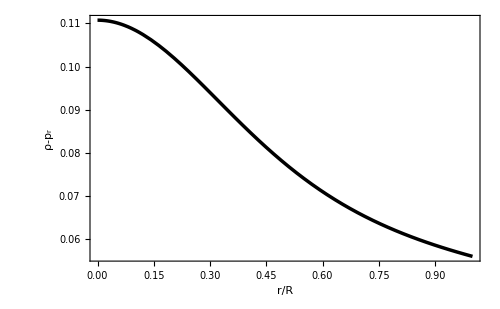

```mathematica
solu1:=Re[dec1[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
dec2[x_]:=ρg[x]-Ptg[x];
```

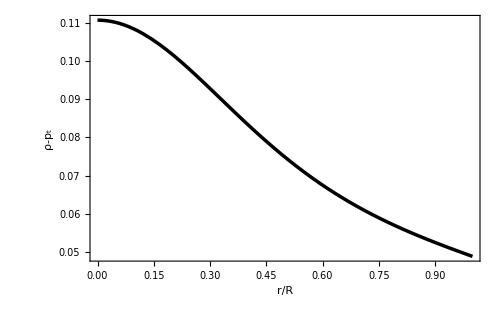

```mathematica
solu1:=Re[dec2[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Condicion de energía fuerte

```mathematica
sec[x_]:=ρg[x]-Prg[x]-2*Ptg[x];
```

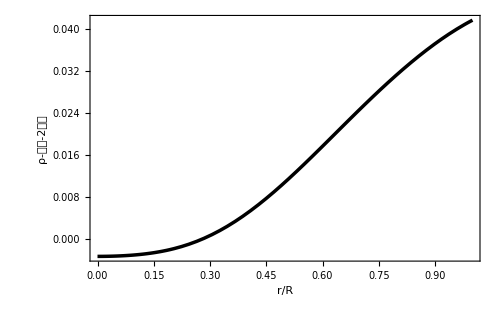

```mathematica
solu1:=Re[sec[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-𝓅𝓇-2𝓅𝓉"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Corrimiento al rojo

```mathematica
Z[r_]:=1/(√(ⅇ^(νnumer[r])))-1
```

```mathematica
Z[r]/.{M-> u R, r->x R}//FullSimplify
```

-1+1./(√((0.233923-1. √(1-2. u)-0.233923 x^2)^2))

```mathematica
Z[x_]:=-1+0.9999999999999998/(√((0.2339234868849825-1. √(1-2. u)-0.2339234868849825 x^2)^2))
```

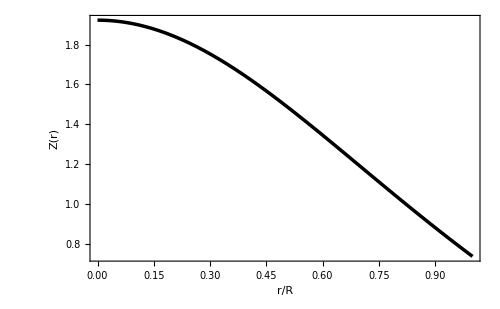

```mathematica
solu1:=Re[Z[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Z(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condición de causalidad:?

#### Velocidad Radial?

```mathematica
vr[r_]:=D[Pr[r],r]/D[ρ[r],r]
```

```mathematica
vr[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.00912757 (0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-1.92371 √(1-2. u)-1.35 x^2) (0.45-1.92371 √(1-2. u)-0.45 x^2) (4.86+((-0.9-1.92371 √(1-2. u))^(2/3) u (0.750343-3.20764 √(1-2. u)-3.75171 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(2/3))+8.33714 (-0.9-1.92371 √(1-2. u))^(2/3) u (0.45-1.92371 √(1-2. u)-1.35 x^2)^(1/3)+0.0000113011 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.233923+1. √(1-2. u)+0.233923 x^2)-(0.0000376703 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.233923-1. √(1-2. u)-0.233923 x^2)^2)/(-0.233923+1. √(1-2. u)+0.389872 x^2)+3.76703×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.233923+1. √(1-2. u)+0.70177 x^2))+0.286479 (0.45-1.92371 √(1-2. u)-1.35 x^2) (-0.81+3.46267 √(1-2. u)+2.43 x^2+8.05185×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.233923+1. √(1-2. u)+0.233923 x^2) (-0.233923+1. √(1-2. u)+0.70177 x^2)+(-0.9-1.92371 √(1-2. u))^(2/3) u (0.45-1.92371 √(1-2. u)-1.35 x^2)^(1/3) (-0.833714+3.56405 √(1-2. u)+4.16857 x^2))+0.859437 (0.45-1.92371 √(1-2. u)-0.45 x^2) (-0.81+3.46267 √(1-2. u)+2.43 x^2+8.05185×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 x^2))/((0.45-1.92371 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.233923+1. √(1-2. u)+0.233923 x^2) (-0.233923+1. √(1-2. u)+0.70177 x^2)+(-0.9-1.92371 √(1-2. u))^(2/3) u (0.45-1.92371 √(1-2. u)-1.35 x^2)^(1/3) (-0.833714+3.56405 √(1-2. u)+4.16857 x^2))))/((-0.9-1.92371 √(1-2. u))^(2/3) u (0.233923-1. √(1-2. u)-0.233923 x^2)^2 (0.0870899-0.372301 √(1-2. u)-0.0870899 x^2))

```mathematica
vr[x_]:= (0.009127572132678053 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2) (0.45-1.9237059347583163 √(1-2. u)-0.45 x^2) (4.86+((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.7503425174639905-3.2076407865488314 √(1-2. u)-3.751712587319952 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(2/3)+8.337139082933227 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(1/3)+0.000011301104319637788 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.23392348688498252+1. √(1-2. u)+0.23392348688498252 x^2)-(0.000037670347732125975 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.23392348688498252-1. √(1-2. u)-0.23392348688498252 x^2)^2)/(-0.23392348688498252+1. √(1-2. u)+0.38987247814163745 x^2)+3.7670347732125963*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 x^2))+0.2864788975654116 (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2) (-0.81+3.4626706825649696 √(1-2. u)+2.43 x^2+8.051852388522243*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2) (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 x^2)+(-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(1/3) (-0.8337139082933227+3.56404531838759 √(1-2. u)+4.1685695414666135 x^2))+0.8594366926962349 (0.45-1.9237059347583163 √(1-2. u)-0.45 x^2) (-0.81+3.4626706825649696 √(1-2. u)+2.43 x^2+8.051852388522243*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 x^2))/(0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 x^2) (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 x^2)+(-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.45-1.9237059347583163 √(1-2. u)-1.35 x^2)^(1/3) (-0.8337139082933227+3.56404531838759 √(1-2. u)+4.1685695414666135 x^2))))/((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.2339234868849825-1. √(1-2. u)-0.2339234868849825 x^2)^2 (0.08708989953535455-0.37230079243037134 √(1-2. u)-0.0870898995353546 x^2))
```

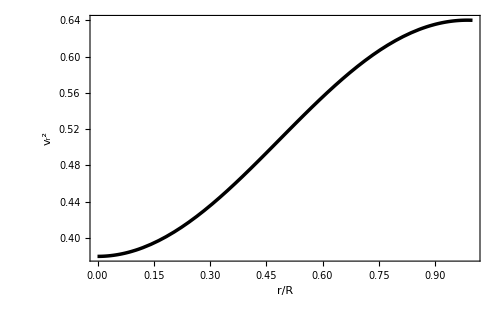

```mathematica
solu1:=vr[x]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Velocidad Tangencial

```mathematica
vt[r_]:=D[Pt[r],r]/D[ρ[r],r]
vt[r]/.{M-> u R, r->x R}
```

(-(0.0397887 (1-1/1)1(11 (1))/(x (1)^2 (1)^2 (1+1)^3)+5+1)/((0.358099 3 (5.79425×10^-8 1-1))/(23 1-1)^(8/3)-(19 3)/1^1)
 |  |  |  |

```mathematica
vt[x_]:={{(-(0.039788735772973836 (1-1/1)1(1 1 (1))/(x (1)^2 (1)^2 (1+1)^3)+5+1)/((0.3580986219567646 3 (5.794250230297304*^-8 1-1))/(23 1-1)^(8/3)-(19 3)/1^1)}, {{{, , , , }}}}
```

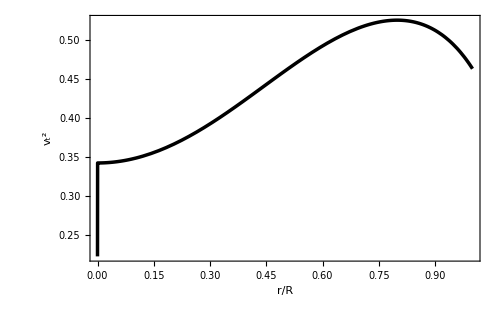

```mathematica
solu1:=Re[vt[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

## Anisotropía

```mathematica
Π[x_]:=Ptg[x]-Prg[x]
```

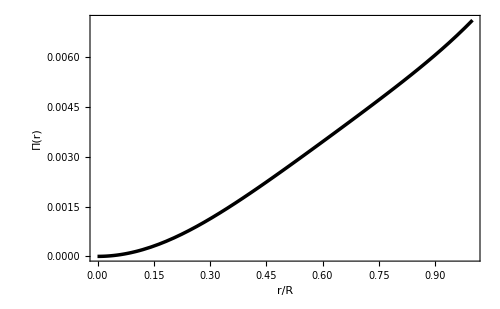

```mathematica
solu1:=Re[Π[x]]/.{u->0.3340789749418907}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Π(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Π[x]/.{x->√(x^2+y^2)}//Simplify
```

-((0.0107518 (-0.81+3.46267 √(1-2. u)+2.43 (x^2+y^2)+8.05185×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2)) (-0.233923+1. √(1-2. u)+0.70177 (x^2+y^2))+(-0.9-1.92371 √(1-2. u))^(2/3) u (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.833714+3.56405 √(1-2. u)+4.16857 (x^2+y^2))))/((-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2)) (-0.233923+1. √(1-2. u)+0.70177 (x^2+y^2))))+(0.000363175 (1-(2. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-23.9802 (x^2+y^2) (0.233923-1. √(1-2. u)-0.70177 (x^2+y^2))^2 (1. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+51.2565 (0.233923-1. √(1-2. u)-0.70177 (x^2+y^2))^2 (-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2)) (1. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.265144 (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-7.11895 (-0.233923+1. √(1-2. u))^3-14.9876 (0.233923-1. √(1-2. u))^2 (x^2+y^2)-8.95966 (-0.233923+1. √(1-2. u)) (x^2+y^2)^2-1.36688 (x^2+y^2)^3+14.2379 (-0.233923+1. √(1-2. u)) (0.233923-1. √(1-2. u)-0.70177 (x^2+y^2))^2-0.00157731 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^2. (-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2))^3)+0.5 (x^2+y^2) (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2))-0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 (x^2+y^2)))^2-4. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.92371 √(1-2. u)-0.45 (x^2+y^2))^2 (4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2))+0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 (x^2+y^2)))-1. (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-1.92371 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2))+0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 (x^2+y^2)))+2. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.92371 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2))+0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 (x^2+y^2)))-1. (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.92371 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (14.8026 (-0.9-1.92371 √(1-2. u))^(2/3) u (0.233923-1. √(1-2. u)-0.233923 (x^2+y^2))^2+6.92534 (-0.233923+1. √(1-2. u)+0.70177 (x^2+y^2)) (1. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2)) (4.18559×10^-6 (((-0.9-1.92371 √(1-2. u))^(2/3) u (1.35-5.77112 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.233923+1. √(1-2. u)+0.233923 (x^2+y^2))+0.283367 (-0.9-1.92371 √(1-2. u))^(2/3) u (-0.233923+1. √(1-2. u)+1.16962 (x^2+y^2))))))/((0.233923-1. √(1-2. u)-0.70177 (x^2+y^2))^2 (0.233923-1. √(1-2. u)-0.233923 (x^2+y^2))^2 (1. (-0.9-1.92371 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.92371 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)

```mathematica
Π[x_,y_]:=-((0.010751839448809199 (-0.81+3.4626706825649696 √(1-2. u)+2.43 (x^2+y^2)+8.051852388522243*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 (x^2+y^2)) (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 (x^2+y^2))+(-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.8337139082933227+3.56404531838759 √(1-2. u)+4.1685695414666135 (x^2+y^2))))/((-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 (x^2+y^2)) (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 (x^2+y^2))))+(0.00036317455583588634 (1-(2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-23.980176511789907 (x^2+y^2) (0.2339234868849825-1. √(1-2. u)-0.7017704606549475 (x^2+y^2))^2 (1. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+51.25645319142468 (0.2339234868849825-1. √(1-2. u)-0.7017704606549475 (x^2+y^2))^2 (-0.23392348688498252+1. √(1-2. u)+0.23392348688498252 (x^2+y^2)) (1. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.26514436682670883 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-7.118951832142317 (-0.2339234868849825+1. √(1-2. u))^3-14.987610319868688 (0.2339234868849825-1. √(1-2. u))^2 (x^2+y^2)-8.95966039113686 (-0.2339234868849825+1. √(1-2. u)) (x^2+y^2)^2-1.366875 (x^2+y^2)^3+14.237903664284634 (-0.2339234868849825+1. √(1-2. u)) (0.2339234868849825-1. √(1-2. u)-0.7017704606549475 (x^2+y^2))^2-0.0015773056131510555 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^2. (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 (x^2+y^2))^3)+0.5 (x^2+y^2) (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 (x^2+y^2))-0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 (x^2+y^2)))^2-4. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.9237059347583163 √(1-2. u)-0.45 (x^2+y^2))^2 (4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 (x^2+y^2))+0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 (x^2+y^2)))-1. (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-1.9237059347583163 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 (x^2+y^2))+0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 (x^2+y^2)))+2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.9237059347583163 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 (x^2+y^2))+0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 (x^2+y^2)))-1. (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.9237059347583163 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (14.80257809369747 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (0.2339234868849825-1. √(1-2. u)-0.2339234868849825 (x^2+y^2))^2+6.925341365129939 (-0.2339234868849825+1. √(1-2. u)+0.7017704606549475 (x^2+y^2)) (1. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2)) (4.18559419245844*^-6 (((-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (1.35-5.771117804274949 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.2339234868849825+1. √(1-2. u)+0.2339234868849825 (x^2+y^2))+0.2833665511290421 (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (-0.2339234868849825+1. √(1-2. u)+1.1696174344249124 (x^2+y^2))))))/((0.2339234868849825-1. √(1-2. u)-0.7017704606549475 (x^2+y^2))^2 (0.2339234868849825-1. √(1-2. u)-0.2339234868849825 (x^2+y^2))^2 (1. (-0.9000000000000001-1.9237059347583163 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.9237059347583163 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)
```

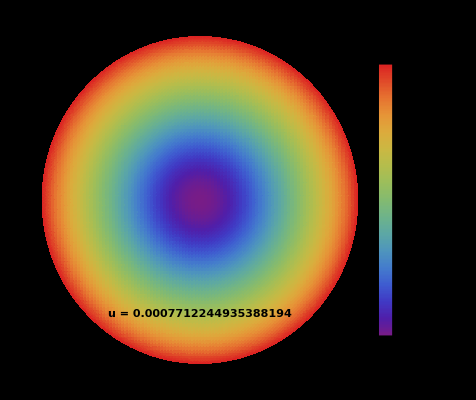

```mathematica
DensityPlot[Re[Π[x,y]]/.{u->0.3340789749418907},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.3340789749418907",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Cracking Gravitacional?

### Falta actualizar desede aqui para abajo, pero no cumple por lo visto en la vt^2

```mathematica
CG[x_]:=vt[x]-vr[x]
```

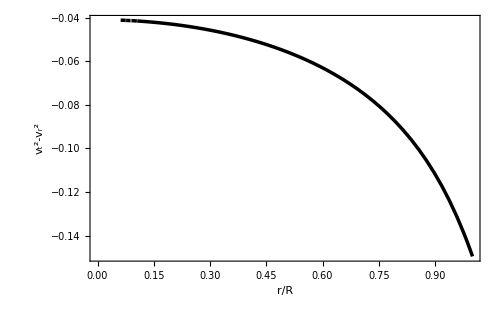

```mathematica
solu1:=CG[x]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2-v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
CG[x]/.{x->√(x^2+y^2)}
```

-((0.00472044 1 (1/π(0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2)) 1 (4.86+1/1+1+1-1/1+5.50302×10^-6 (1/1)^3. (-0.198372+1. √(1-2. u)+0.595116 (x^2+y^2)))+1+0.859437 (0.45-1-0.45 (1)) (-0.81+3+(-0.9-2.26846 √(1-2. u))^(2/3) u (0.45-1-1)^(1/3) (-0.829352+4.18079 √(1-2. u)+4.14676 (x^2+y^2)))))/((-0.9-2.26846 √(1-2. u))^(2/3) u (0.198372-1. √(1-2. u)-0.198372 (x^2+y^2))^2 (0.0626299-0.315719 √(1-2. u)-0.0626299 (x^2+y^2))))-(0.000917315 (0.45-2.26846 1-1.35 (x^2+y^2))^(2/3) (1)^2 (7+1))/((-0.9-2.26846 √(1-1))^(2/3) u √(x^2+y^2) (20-1-1) (1)^3 (1)^3 (1. 1 u (x^2+y^2)-0.5 1)^3)
 |  |  |  |

```mathematica
CG2d[x_,y_]:={{-((0.004720439574565849 1 (1/π(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2)) 1 (4.86+1/1+1+1-1/1+5.503022504604416*^-6 (1/1)^3. (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 (x^2+y^2)))+1+0.8594366926962349 (0.45-1-0.45 (1)) (-0.81+3+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.45-1-1)^(1/3) (-0.8293524416135881+4.180791470620436 √(1-2. u)+4.1467622080679405 (x^2+y^2)))))/((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 (x^2+y^2))^2 (0.06262985035679756-0.3157190249159851 √(1-2. u)-0.06262985035679754 (x^2+y^2))))-(0.0009173153429009489 (0.45-2.2684640056268837 1-1.35 (x^2+y^2))^(2/3) (1)^2 (7+1))/((-0.9000000000000001-2.2684640056268837 √(1-1))^(2/3) u √(x^2+y^2) (20-1-1) (1)^3 (1)^3 (1. 1 u (x^2+y^2)-0.5 1)^3)}, {{{, , , , }}}}
```

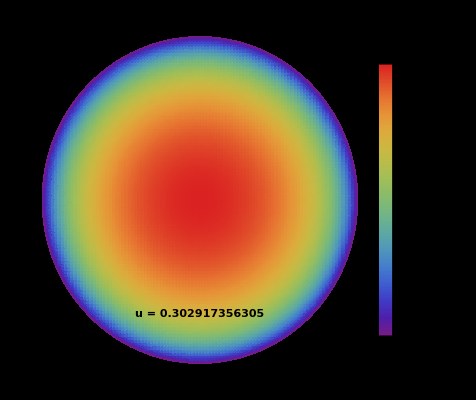

```mathematica
DensityPlot[Re[CG2d[x,y]]/.{u->0.302917356305},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.302917356305",Large,Bold],{0,-0.7}],PlotPoints->100]
```